# Vessel Segmentation of Retinal Fundus Images

Name: Tingting Huang

Instructor: Etienne Bernard

Wolfram Science Summer School 2015

## Homework Solution

Rule Number: 689842260

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{689842260,{3,1},{1,1}},{{{2}},0},{{{n}}}]],{n,0,200,1}]
```

```mathematica
ArrayPlot[CellularAutomaton[{689842260,{3,1},{1,1}},{{{2}},0},{100,All,All}][[All,100]]]
```

-Graphics-

I found this rule number 689842260 would produce an image which is non-square and shrinking as step increases. By non-square, it means the image is not occupying the whole square space like a carpet. The initial condition is a single black cell at the center.

### Claim

The occupied area of the CA Image of this particular rule is decreasing from 100 to 150 steps

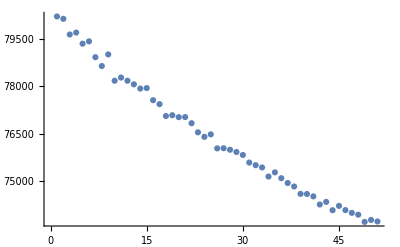

```mathematica
arealist=Table[Total[ImageData[Binarize[ImageConvolve[GradientFilter[Image[ArrayPlot[CellularAutomaton[{689842260,{3,1},{1,1}},{{{2}},0},{{{x}}}]]],1], BoxMatrix[3]]]],2],{x,100,150,1}];
ListPlot[arealist]
```

## Project Description

The leading causes of irreversible blindness in the United States are mainly age-related macular degeneration, cataract, and glaucoman [1]. Early detection of these diseases is important for patients to optimize their treatment benefits. Among many imaging modalities used for retina like Optical Coherence Tomography (OCT), fundus photography is one of the most commonly adopted methods for ophthalmologists to detect and assess symptoms of eye diseases. The existing algorithms for automatic fundus image analysis can segment and measure the retinal vasculature, which is a major indicator of various diseases [2,3,4]. However, existing methods usually utilize filters on global fundus image to segment retinal vasculature as a whole, which will have insufficient information about local vessel network. Therefore, our project aims at developing a novel machine-learning algorithm to separate and rebuild a vessel starting from specific points generated by user interface.

Sample color fundus image with manually selected vessel structure. DRIVE database [5].

## Data

Fundus images are obtained from DRIVE database [5].

Healthy eye vs. diseased eye

```mathematica
im1=-Graphics-
```

-Graphics-

## Methods

### Unit Rectangle

#### Preprocessing

```mathematica
gray1=ColorConvert[im1,"Grayscale"]
```

-Graphics-

After convert the color to grayscale, we want to use unit rectangle with given width and length to trace the dark vessels. By minimizing the total pixel value selected in each unit rectangle, we are able to pick out all the desired pixels along the vessel.

```mathematica
Show[gray1, Graphics[{Red,PointSize[0.01],Point[{371,200}]}]]
```

-Graphics-

For an example, starting at position (371, 200) with an initial angle at (2π)/3, method one will change the color of the dark pixels to red.

#### Code

```mathematica
cropAt[image_, position_, length_] := Module[
	{left,right,up,down,crop,postable},
	left = position[[1]]-2*length;
	right = position[[1]]+2*length;
	up = position[[2]]+2*length;
	down = position[[2]]-2*length;
	crop = ImageTake[image,{down,up},{left,right}];
	postable = Flatten[Table[{i,j},{i,left,right},{j,down,up}],1]
];

unitRectangle[image_, theta0_, position_, width_, length_]:= Module[
	{postable},
	postable = cropAt[image,position,length]; 
	Select[postable,isInside[position,#,theta0,width,length]&]
];

isInside[x0_, x_, theta_, width_, length_] := Module[
	{u, v, diff, proj},
	diff = x-x0;
	u = {Cos[theta], Sin[theta]};
	v = {Sin[theta], -Cos[theta]};
	proj = {diff.u, diff.v};
	And[
		0<=First[proj]<=length
		,
		-width/2<=Last[proj]<=+width/2
	]
];

updateAngle[image_, theta0_, position_, width_, length_, stepsize_]:= Module[
	{postable,recs,index},
	postable = cropAt[image,position,length];
	recs = Select[Table[Select[postable,isInside[position,#,x,width,length]/.x->n &],{n,theta0-Pi/2,theta0+Pi/2,stepsize}],#≠{}&];
	index = First[Ordering[Total[PixelValue[image,#]&/@recs,{2}]]];
	theta0-Pi/2+(index-1)*stepsize
];

updatePosition[position_, theta_, length_] := Module[
	{p1,p2,np1,np2},
	p1 = position[[1]];
	p2 = position[[2]];
	np1 = p1+length Cos[theta];
	np2 = p2+length Sin[theta];
	{np1,np2}
];

updateImage[image_, position_, theta_, unitrec_, width_, length_, stepsize_,updatenumber_] := Module[
	{pos,th,rec,pv,change},
	pos = Append[{},position];
	th = Append[{},theta];
	rec = Append[{},unitrec];
	Do[pos = Append[pos,updatePosition[pos[[k]],th[[k]],length]];
		th = Append[th,updateAngle[image,th[[k]],pos[[k+1]],width,length,stepsize]];
	   rec = Join@Append[rec,unitRectangle[image,th[[k+1]],pos[[k+1]],width,length]],
		{k,updatenumber}];
	{pos,th,rec}

];

viewVesselOnImage[image_, position_, theta_, width_, length_, stepsize_,updatenumber_] := Module[
	{update, unitrec, pos, th, rec, pv, blank, change, vessel, g},
	unitrec = unitRectangle[image, theta, position, width, length];
	update = updateImage[image, position, theta, unitrec, width, length, stepsize, updatenumber];
	pos = Floor@update[[1]];
	th = N@update[[2]];
	rec = Floor@update[[3]];
	rec = Flatten[rec,1];
	pv = PixelValue[image,rec];
	change = Table[rec[[n]]->pv[[n]],{n,1,Length[pv]}];
	blank = Image[ConstantArray[1,Reverse@ImageDimensions[image]]];
	vessel = ReplacePixelValue[image,rec->Red]
];
```

#### Result

```mathematica
viewVesselOnImage[gray1,{371,200},N[2Pi/3],2,4,0.1, 100]
```

-Graphics-

```mathematica
AbsoluteTiming[viewVesselOnImage[gray1,{371,200},N[2Pi/3],2,4,0.1, 100]]
```

{41.904,-Graphics-}

Changing the length and width of the unit rectangle will influence the result. On the other hand, smaller step size can lead to better approximation by improving the outcome of the minimizing total pixel value in each unit rectangle, but it can also increase the running time, which is already 44 seconds for just 100 steps.

### Vessel Walls Tracing

#### Preprocessing

```mathematica
grad=ImageAdjust[GradientFilter[im1,1],{.1,10}]
```

-Graphics-

In order to improve the running time, we apply gradient filter on the original image, and try to trace the vessel on the white vessel walls with an initial angle.

We generate random angles for each step based on normal distribution.

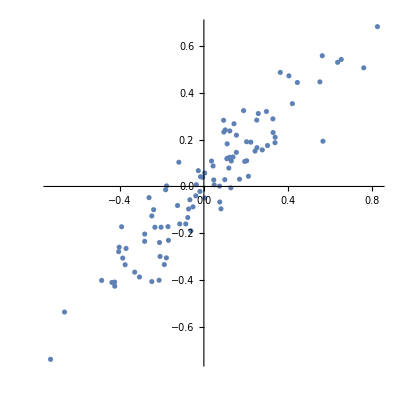

```mathematica
ListPlot[generateRandomSamples[0.25,0.95, 100],AspectRatio->1]
```

We optimize the cost function for every two steps to foresee the growing trend.

Cost Funciton( θ_1,θ_2) =-∑(pixel value)+λ/L^2((θ_1-θ_01)^2+(θ_2-θ_02)^2)+μ/L^2(θ_2-θ_1)^2+(γ(r-r_0))^2

where λ is the curvature constraint, μ is the expansion constraint, γ is the diameter constraint, r is the distance between each pair of pixels, and r_0 is the anticipated vessel diameter.

(Possibly with solving differential equations with respect to each constraint parameters.)

#### Code

```mathematica
endpixel[pixel1_, theta_, l_] := Round[pixel1+l*{Cos[theta], Sin[theta]}];

generateRandomSamples[std_, corr_, n_] := Module[
	{dist},
	dist = MultinormalDistribution[
		{0, 0},
		{{std^2, (corr*std)^2}, {(corr*std)^2, std^2}}
	];
	RandomVariate[dist, n]
];

Clear[findPath]
Options[findPath] = {
	"Length" -> 5,
	MaxIterations -> 10,
	"CurvatureConstraint" -> 0,
	"DiameterConstraint" -> 0,
	"ExpansionConstraint" -> 0,
	"VesselDiameter" -> 4.5,
	"SearchDepth" -> 2,
	"SampleNumber" -> 100
};

findPath[image_, {pixel01_, pixel02_}, {theta01_, theta02_}, opts:OptionsPattern[]] := Module[
	{steptheta, th1, th2, pixel1, pixel2, l, pos, theta, c, cells, samples, ns, costs, dim, depth, inttheta, intpixels, costs2},
	c = OptionValue["CurvatureConstraint"];
	pos = {{pixel01, pixel02}};
	theta = {{theta01, theta02}};
	l = OptionValue["Length"];
	depth = OptionValue["SearchDepth"];
	
	samples = generateRandomSamples[0.2, 0.95, {depth, OptionValue["SampleNumber"]}];
	
	ns = Length[samples[[1]]];
	dim = ImageDimensions[image]-l-1;
	Do[
		If[Or @@ Map[Negative, dim - pos[[k, 1]]], Break[]];
		If[Or @@ Map[Negative, dim - pos[[k, 2]]], Break[]];
		costs = listableCost[
			theta[[k]] + Transpose[samples[[1]]],
			Transpose@Table[theta[[k]], {ns}],
			Transpose@Table[pos[[k]], {ns}],
			image,
			"CurvatureConstraint" -> c,
			"ExpansionConstraint" -> OptionValue["ExpansionConstraint"],
			"DiameterConstraint" -> OptionValue["DiameterConstraint"],
			"Length" -> l,
			"VesselDiameter" -> OptionValue["VesselDiameter"]
		];
		inttheta = (# + theta[[k]]) & /@ samples[[1]];
		intpixels = computePixels[pos[[k]], #, l] & /@ inttheta;
		costs2 = listableCost[
			Transpose[inttheta + samples[[2]]], 
			Transpose@inttheta,
			Transpose@intpixels,
			image,
			"CurvatureConstraint" -> c,
			"ExpansionConstraint" -> OptionValue["ExpansionConstraint"],
			"DiameterConstraint" -> OptionValue["DiameterConstraint"],
			"Length" -> l,
			"VesselDiameter" -> OptionValue["VesselDiameter"]
		];
		costs = costs + 0.7*costs2;
		{th1, th2} = theta[[k]] + First@samples[[1, Ordering[costs, 1]]];
		{pixel1, pixel2} = computePixels[pos[[k]], {th1, th2}, l];

		pos = Append[pos, {pixel1, pixel2}];
		theta = Append[theta, {th1, th2}]
		,
		{k, OptionValue[MaxIterations]}
	];
	{pos, theta}
];

computePixels[pos_, theta_, l_] := Module[
	{u, pixel1, pixel2, diff, proj},
	u = #[Mean[theta]] & /@ {Cos, Sin};
	pixel1 = endpixel[pos[[1]], theta[[1]], l];
	pixel2 = endpixel[pos[[2]], theta[[2]], l];
	diff = pixel2-pixel1;
	proj = diff.u;
	pixel1 = endpixel[pos[[1]], theta[[1]], l + proj/2];
	pixel2 = endpixel[pos[[2]], theta[[2]], l - proj/2];
	{pixel1, pixel2}
];

Clear[listableCost]
Clear[ilistableCost]
Options[listableCost] = {
	"Length" -> 5,
	"CurvatureConstraint" -> 0,
	"ExpansionConstraint" -> 0,
	"DiameterConstraint" -> 0,
	"VesselDiameter" -> 4.5
};
listableCost[{theta1_, theta2_}, {theta01_, theta02_}, {pixel01_, pixel02_},
	imagegradient_, opts:OptionsPattern[]] := Module[
	{c1, c2, l, totalcost, lambda, mu, gamma,pdist},
	l = OptionValue["Length"];
	lambda = OptionValue["CurvatureConstraint"];
	mu = OptionValue["ExpansionConstraint"];
	gamma = OptionValue["DiameterConstraint"];
	c1 = ilistableCost[imagegradient, pixel01, theta1, l];
	c2 = ilistableCost[imagegradient, pixel02, theta2, l];
	
	totalcost = -(c1+c2);
	totalcost = totalcost + lambda/l^2*((theta1-theta01)^2 + (theta2-theta02)^2);
	totalcost = totalcost + mu/l^2*(theta2-theta1)^2;
	pdist = pixelDistance[{pixel01, pixel02}, {theta1, theta2}, l];
	totalcost = totalcost + gamma*(pdist-OptionValue["VesselDiameter"])^2;
	totalcost = MapThread[If[2.<#1<8., #2, #2+10^4.] &, {pdist, totalcost}];
	totalcost
];

ilistableCost[image_, pixel0_, theta_, l_] := Module[
	{pixel, pos, val, dim, imagedata},
	pixel = endpixel[pixel0, theta, l];
	pos = MapThread[getLinePixelPositions, {pixel0, pixel}];

	dim = ImageDimensions[image];
	pos = Reverse[Transpose[#]] & /@ pos;
	pos[[All, 1]] = dim[[2]] - pos[[All, 1]];
	pos = Transpose /@ pos;
	imagedata = ImageData[image];
	val = Extract[imagedata, #] & /@ pos;
	(Total /@ val)/l
];

pixelDistance[{pixel01_,pixel02_}, {theta01_List, theta02_List}, length_] := Module[
	{pixel1,pixel2},
	pixel1 = endpixel[pixel01, theta01, length];
	pixel2 = endpixel[pixel02, theta02, length];
	N[Norm /@ (pixel2-pixel1)]

];

endpixel[pixel1_, theta_, l_] := Round[pixel1+l*{Cos[theta], Sin[theta]}];
endpixel[pixel1_, theta_List, l_] := Round[pixel1+l*Transpose[{Cos[theta], Sin[theta]}]];

getLinePixelPositions[pixel0_, pixel_] := Module[
	{pos, posrev},
	pos = igetLinePixelPositions[pixel0, pixel];
	posrev = Reverse /@ igetLinePixelPositions[Reverse[pixel0], Reverse[pixel]];
	Union[pos, posrev]
];

igetLinePixelPositions[pixel0_, pixel_] := Module[
	{diff, slope, xlist, ylist},
	diff = pixel - pixel0;
	If[diff[[1]]==0, Return[{}]];
	slope = diff[[2]]/diff[[1]];
	xlist = Range @@ Sort[{0, diff[[1]]}];
	ylist = Round[xlist*slope];
	Transpose[{xlist, ylist} + pixel0]
];

Clear[viewVesselOnImage3]
Options[viewVesselOnImage3] = {
	"Length" -> 5,
	MaxIterations -> 10,
	"CurvatureConstraint" -> 0,
	"DiameterConstraint" -> 0,
	"ExpansionConstraint" -> 0,
	"VesselDiameter" -> 4.5
};
viewVesselOnImage3[image_, {pixel01_, pixel02_}, {theta01_, theta02_}, opts:OptionsPattern[]] := Module[
	{pos, pixelPositions, theta},
	{pixelPositions, theta} = findPath[image, Round[{pixel01, pixel02}], {theta01, theta02},
						"CurvatureConstraint" -> OptionValue["CurvatureConstraint"],
						"ExpansionConstraint" -> OptionValue["ExpansionConstraint"],
						"DiameterConstraint" -> OptionValue["DiameterConstraint"],
						"Length" -> OptionValue["Length"],
						MaxIterations -> OptionValue[MaxIterations],
						"VesselDiameter" -> OptionValue["VesselDiameter"]
					];
	pos = {#1,Reverse[#2]} & @@@ Partition[pixelPositions, 2, 1];
	pos = Partition[Flatten[#, 1], 2, 1, 1] & /@ pos;
	Show[image, Graphics[{EdgeForm[Opacity[0.6,Red]], Opacity[0], Polygon /@ pos}]]
	
];

locatorIcon[pos_, r_, color_] := Graphics[
		{color, Opacity[0.5], Circle[pos,r], 
		Line[pos+r*# & /@ {{-1.,0.},{1.,0.}}],
		Line[pos+r*# & /@{{0.,-1.},{0.,1.}}]}
];

findAngle[p1_, p2_, p3_] := Module[
	{angle},
	angle = ConstantArray[N[ArcTan[(p3-Mean[{p1,p2}])[[1]],(p3-Mean[{p1,p2}])[[2]]]],2];
	angle
];

endpixel2[pixel1_, theta_, l_] := Round[pixel1-l*{Cos[theta], Sin[theta]}];

Clear[g,interface]
interface[image_] := 
	Manipulate[
		Style[Show[g, 
			locatorIcon[p1, 1.6, Red],
			locatorIcon[p2, 1.6, Red],
			locatorIcon[p3, 1.6, Blue],
			Graphics[{
				Red, Line[{p1, endpixel2[p1,findAngle[p1,p2,p3][[1]],length]}],
						Line[{p2, endpixel2[p2,findAngle[p1,p2,p3][[1]],length]}]
				},PlotRange->All]
			], Magnification->magnification],
		{{p1,{10,10}},Locator,Appearance->None},
		{{p2,{20,20}},Locator,Appearance->None},
		{{p3,{30,30}},Locator,Appearance->None},
		Button["Start",
			g= viewVesselOnImage3[image,{p1,p2},findAngle[p1,p2,p3], 
				"CurvatureConstraint"->curvatureConstraint,
				"ExpansionConstraint"->expansionConstraint,
				"DiameterConstraint"->diameterConstraint, 
				"VesselDiameter"->vesselDiameter,
				MaxIterations->iteration, 
				"Length"->length
			];
		],
		{{curvatureConstraint,1.5},0,10,0.5},
		{{expansionConstraint,4},0,10,1},
		{{diameterConstraint,0.02},0,0.1,0.01},
		{{vesselDiameter,4.5},2,7,0.5},
		{{iteration,50},1,100,5},
		{{length,5},1,10,1},
		{{magnification,3},1,10},
		ControlPlacement->Left
	];
```

#### Result

The demonstration will be shown on a portion of the filtered image.

```mathematica
gradzoom=ImageTake[grad,{1,200},{100,400}]
```

-Graphics-

The way of using the user interface is:
1. Click “Start” button.
2. Move two red dots at each side of desired vessel.
3. Move the blue dot so that the two short lines on each red dots align with the vessel walls. 
4. Press “Start” to see the result with default settings.
5. Adjust the parameters to get the best result.

```mathematica
interface[gradzoom]
```

## Conclusions

The user needs to select two points at each side of one vessel (red dots), and a third position to indicate an initial angle (blue dot). By changing the constraint parameters on curvature, expansion, and diameter, our model can trace the vessel without the disturbance of other branching vessels.

## Future Directions

Ideally, the constraint parameters can be optimized automatically. It would be more useful for ophthalmologists if future project can specify branching network, and compute measurements for targeted pathologies with high accuracy. The results of future algorithm will be compared with standard references marked by trained clinicians. We can possibly apply the same technique to 3D OCT image to reconstruct 3D vessel structure.

## References

[1] The Eye Diseases Prevalence Research Group*. Causes and Prevalence of Visual Impairment Among Adults in the United States. Arch Ophthalmol. 2004;122(4):477-485. doi:10.1001/archopht.122.4.477.
[2] Odstrcilik, J.; Kolar, R.; Budai, A.; Hornegger, J.; Jan, J.; Gazarek, J.; Kubena, T.; Cernosek, P.; Svoboda, O.; Angelopoulou, E., “Retinal vessel segmentation by improved matched filtering: evaluation on a new high-resolution fundus image database,” Image Processing, IET , vol.7, no.4, pp.373,383, June 2013
[3] Marin, D.; Aquino, A.; Gegundez-Arias, M.E.; Bravo, J.M., “A New Supervised Method for Blood Vessel Segmentation in Retinal Images by Using Gray-Level and Moment Invariants-Based Features,” Medical Imaging, IEEE Transactions on , vol.30, no.1, pp.146,158, Jan. 2011
[4] Staal, J.; Abramoff, M.D.; Niemeijer, M.; Viergever, M.A.; van Ginneken, B., “Ridge-based vessel segmentation in color images of the retina,” Medical Imaging, IEEE Transactions on , vol.23, no.4, pp.501,509, April 2004
[5] Sample color fundus image with manually selected vessel structure. DRIVE database.
J.J. Staal, M.D. Abramoff, M. Niemeijer, M.A. Viergever, B. van Ginneken, “Ridge based vessel segmentation in color images of the retina”, IEEE Transactions on Medical Imaging, 2004, vol. 23, pp. 501-509.

## Other

Last Modified: Thursday, July 16, 2015

"Insert date..."